## Forced Harmonic Oscillator

```mathematica
a=With[{tf=100,k=1,m=1,c=0.1},sol2=ParametricNDSolve[{m x''[t]+c x'[t]+k x[t]==Sin[ω t],x[0]==1,x'[0]==0},{x,x'},{t,0,tf},{ω}];
Manipulate[Animate[Column[{Show[Graphics[Rectangle[{x[ω][t]/.sol2/.t->tval,0}],PlotRange->{{-4,4},{-0.5,1.8}},AspectRatio->Automatic],With[{xf=x[ω][t]/.sol2/.t->tval,n=4},Plot[0.5+0.2Sin[(2π n)/xf(x)],{x,0,xf},Axes->False]],Graphics@Text[Style["Forced simple harmonic oscillator",FontSize->12],{0,1.4}]],Plot[{Sin[ω t],x[ω][t]/.sol2},{t,Ti,T},PlotStyle->{{Thin,Blue},Red},AxesLabel->(Style[#,FontSize->16]&/@{"t","x"}),PlotRange->{All,{-2,2}},PlotLegends->Placed[{"Forcing","response"},{0.5,0}]],Show[ParametricPlot[{x[ω][t],x'[ω][t]}/.sol2,{t,Ti,T},PlotRange->{-2,2},AxesLabel->(Style[#,FontSize->16]&/@{"x","ẋ"}),PlotPoints->100],ListPlot[{{{x[ω][Ti],x'[ω][Ti]}/.sol2},{{x[ω][T],x'[ω][T]}/.sol2}},PlotMarkers->{"●",Medium},PlotStyle->{Green,Red}]]}],{tval,0,T}],{ω,0,5},{T,10,tf},{Ti,0,0.99T}]
]
```

```mathematica
(*CloudDeploy[a]*)
```

CloudObject[https://www.wolframcloud.com/obj/0c95b787-9976-4a52-b90c-24cc2dbeaafc]

### Static plots

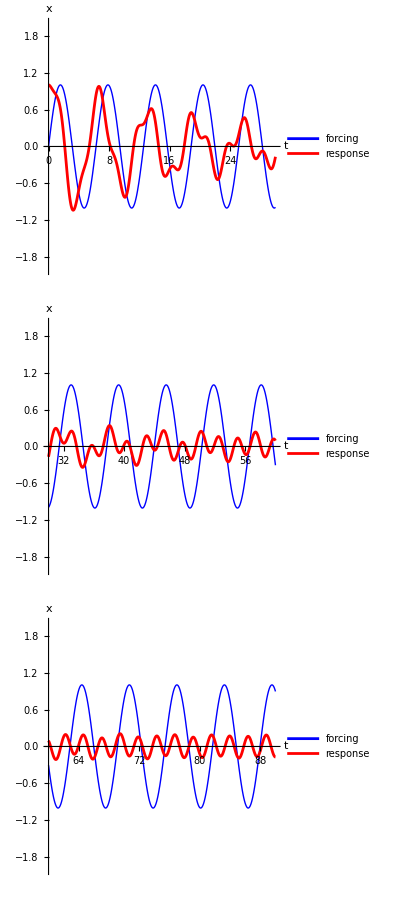

```mathematica
Column[Table[Plot[{Sin[1 t],x[2.6][t]/.sol2},{t,i,i+30},AspectRatio->1/2,AxesLabel->(Style[#,FontSize->14,FontFamily->"EB Garamond"]&/@{"t","x"}),PlotLegends->Placed[LineLegend[{"forcing","response"},LegendLayout->"Row"],{0.5,0.9}],PlotRange->{All,{-2,2}},PlotStyle->{{Thin,Blue},Red}],{i,{0,30,60}}]]
```

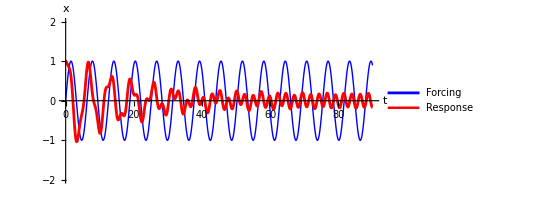

/Users/emasroo1/Library/CloudStorage/GoogleDrive-emasroo1@swarthmore.edu/My Drive/Teaching/Spring 2025/E91/Demonstrations/Limit Cycles/limitcycle1.png

```mathematica
Plot[{Sin[1 t],x[2.6][t]/.sol2},{t,0,90},AspectRatio->1/2,AxesLabel->(Style[#,FontSize->14,FontFamily->"EB Garamond"]&/@{"t","x"}),PlotLegends->Placed[LineLegend[(Style[#,FontSize->14,FontFamily->"EB Garamond"]&/@{"Forcing","Response"}),LegendLayout->"Row"],{0.5,0.9}],PlotRange->{All,{-2,2}},PlotStyle->{{Thin,Blue},{Thickness[0.005],Red}},TicksStyle->Directive["Label", FontSize->14,FontFamily->"EB Garamond"]]
Export[NotebookDirectory[]<>"limitcycle1.png",%]
```

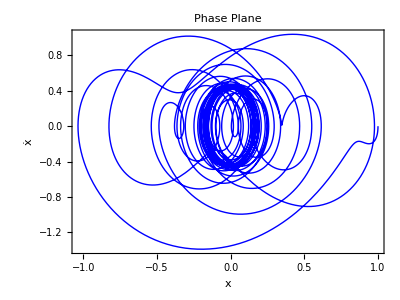

/Users/emasroo1/Library/CloudStorage/GoogleDrive-emasroo1@swarthmore.edu/My Drive/Teaching/Spring 2025/E91/Demonstrations/Limit Cycles/limitcycle2.png

```mathematica
ParametricPlot[{x[2.6][t]/.sol2,x'[2.6][t]/.sol2},{t,0,90},AspectRatio->3/4,Frame->True,PlotLabel->Style["Phase Plane",FontSize->18,FontFamily->"EB Garamond"],FrameLabel->(Style[#,FontSize->18,FontFamily->"EB Garamond"]&/@{"x","ẋ"}),PlotRange->All,PlotStyle->{Thin,Blue},FrameTicksStyle->Directive["Label", FontSize->16,FontFamily->"EB Garamond"]]
Export[NotebookDirectory[]<>"limitcycle2.png",%]
```